## Data Handling

```mathematica
Clear["Global`*"]
```

System & Directory

```mathematica
os = "linux";
baselinux = "~/repos/fp/FKO";
basewin = "D:\\Git\\F-Praktikum\\AFM";                   (* vergiss nicht den backslash mit backslash zu escapen!!!*)
subdir = "data-plots";
If[os == "linux", 
	slash = "/"; basedir = baselinux,  (* THEN *)
	slash = "\\";basedir = basewin]       (* ELSE *);
```

```mathematica
SetDirectory[basedir<>slash<>subdir];
fnames= FileNames["*.dpt"];
```

```mathematica
(* For[i = 1, i < Length[fnames] + 1, i++, Print[i, ": ", fnames⟦i⟧]]; *)
```

```mathematica
data[num_] :=Import[fnames⟦num+1⟧, "Table"]
```

```mathematica
dat0=data[0];
```

```mathematica
SetOptions[ListPlot,Frame->True,Joined->True,ImageSize->1000];
```

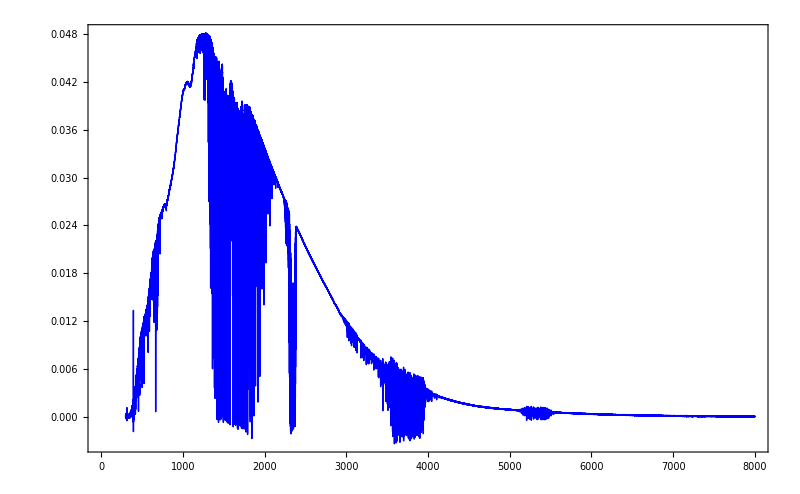

```mathematica
ListPlot[dat0]
```